================= Starting part 1 of 121 =================

New best result: {980.295,{0.000359236,-1.3683×10^-6}}

New best result: {964.847,{0.00245194,0.499991}}

New best result: {920.9,{0.0047033,0.999984}}

New best result: {831.589,{0.00722157,1.49998}}

New best result: {640.069,{0.0105167,2.00002}}

New best result: {237.585,{0.0153694,2.50015}}

New best result: {40.7542,{0.018477,2.99996}}

================= Starting part 50  of 121 =================

================= Starting part 100  of 121 =================

===================== END =====================

Found best params {0.018477,2.99996} with error 40.7542

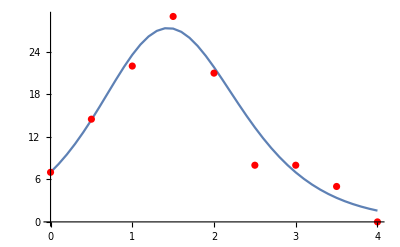

Expected from book (with {0.0178,2.73}):

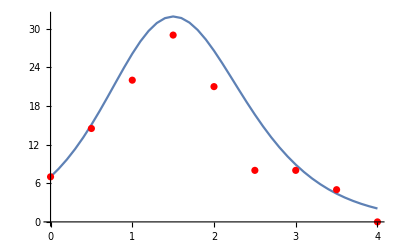

```mathematica
Clear["Global`*"];

(*This derivativeDelta shouldn't be chosen too low, because the machine won't be able to handle such small values.*)
derivativeDelta=10^(-6);

der[h_,x_,y_]:=(
xDer=(h[x+derivativeDelta,y]-h[x-derivativeDelta,y])/(2 *derivativeDelta);
yDer=(h[x,y+derivativeDelta]-h[x,y-derivativeDelta])/(2*derivativeDelta);
{xDer,yDer}
);

GradientDescent[f_,startingX_,startingY_,inputStep_,tolerance_]:=(
minStep = 10^(-10);
currentX=startingX;
currentY=startingY;
{currentDerX, currentDerY}=der[f,currentX,currentY];
currentIter=1;
maxIter=10000;
lastChangeX=tolerance+1;
lastChangeY=tolerance+1;
step=inputStep;
(*startingZ=f[startingX,startingY];
Print["Starting position: ", {currentX, currentY}, ". Starting derivatives: ", {currentDerX, currentDerY},". Starting value: ",startingZ,". Used step: ", step,". Max iterations: ", maxIter];*)

While[step≥minStep&&currentIter<=maxIter && (Abs[lastChangeX]≥tolerance||Abs[lastChangeY]≥tolerance),
step=inputStep;
newX = currentX-currentDerX*step;
newY = currentY-currentDerY*step;
currentZ=f[currentX,currentY];
newZ=f[newX,newY];

While[newZ>currentZ&&step≥minStep,
newX = currentX-currentDerX*step;
newY = currentY-currentDerY*step;
step/=2.;
newZ=f[newX,newY];
];

lastChangeX=newX-currentX;
lastChangeY=newY-currentY;
	currentX=newX;
	currentY=newY;
	currentIter++;

	{currentDerX, currentDerY}=der[f,currentX,currentY];
(*If[Mod[currentIter,1000]==0,Print["(Iteration ",currentIter,") Position: ", {currentX, currentY}, " with value ",newZ,". Derivatives: ",{currentDerX, currentDerY},". Used step: ", step,". Tolerance: ", tolerance, ". Last changes: ", {lastChangeX, lastChangeY},"."]];*)
];

(*Print["Ended on iteration ",currentIter," (of max ", maxIter,") with value ",newZ,", with derivatives ",{currentDerX,currentDerY},", step ", step, "(below minStep: ",step<minStep,"), and last changes ", {lastChangeX, lastChangeY}, " (below tolerance: ", {lastChangeX< tolerance, lastChangeY < tolerance}, ")"];*)

{newZ,{currentX,currentY}}
);

euler[beta_,gamma_]:=(
For[k=0,k≤dataLength,k++,sderivative=-beta sdata[k]idata[k];sdata[k+1]=sdata[k] + sderivative*delta;
                                                                           iderivative=   beta sdata[k]idata[k]-gamma idata[k];idata[k+1]=idata[k]+iderivative*delta];
iTable=Table[{k*delta, idata[k]},{k,0,dataLength}];
interpolatedI=Interpolation[iTable,InterpolationOrder->1];
);

eulerError[beta_?NumericQ,gamma_?NumericQ]:=(
(* Hide messages for overflowing *)
Quiet[

euler[beta, gamma];
Sum[(importedIData[[k+1]]-interpolatedI[k*1/2])^2,{k,0,rangeEnd}]

,General::ovfl]
);

GradientDescentRange[f_,rangeX_,rangeY_,rangeStep_]:=(
params=Table[{b,g},{b,rangeX[[1]],rangeX[[2]],rangeStep},{g,rangeY[[1]],rangeY[[2]],rangeStep}];
params = Flatten[params, 1];

bestParams={0,0};
bestValue = Infinity;
Print["================= Starting part 1 of ",Length[params]," ================="];

For[i=1,i≤Length[params],i++,
If[Mod[i,50]==0,
Print["================= Starting part ",i" of ",Length[params]," ================="]];

{x,y} = params[[i]];
result=GradientDescent[eulerError,x,y,10.^(-7),0.0001];
resultValue=result[[1]];

If[resultValue<bestValue,
Print["New best result: ", result];
bestValue=resultValue;
bestParams=result[[2]];
];
];

Print["===================== END ====================="];
{bestValue,bestParams}
);

importedIData={7,14.5,22,29,21,8,8,5,0};
importedSData={254,235,201,153.5,121,108,97,90,83};

n=importedIData[[1]]+importedSData[[1]];
rangeEnd=Length[importedIData]-1;
delta=0.1;
dataLength=rangeEnd/delta;

idata[0]=importedIData[[1]];
sdata[0]=importedSData[[1]];

rangeEnd = Length[importedIData]-1; 
delta=0.1;
dataLength= rangeEnd/delta;

(* Minimize error *)
{bestError,{beta,gamma}} = GradientDescentRange[eulerError,{0.,5.},{0.,5.},0.5];

(* Plot output *)
Print["Found best params ", {beta,gamma}, " with error ",bestError];
euler[beta,gamma];
generatedPlot =ListPlot[Table[{k*delta, idata[k]},{k,0,dataLength*1/2}],PlotRange->All,Joined->True];
inputPlot=ListPlot[Table[{k*1/2,importedIData[[k+1]]},{k,0,rangeEnd}],PlotRange->All,PlotStyle->Red];
Show[generatedPlot,inputPlot,PlotRange->All]

Print["Expected from book (with ",{0.0178,2.73},"):"];
euler[0.0178,2.73];
generatedPlot =ListPlot[Table[{k*delta, idata[k]},{k,0,dataLength*1/2}],PlotRange->All,Joined->True];
inputPlot=ListPlot[Table[{k*1/2,importedIData[[k+1]]},{k,0,rangeEnd}],PlotRange->All,PlotStyle->Red];
Show[generatedPlot,inputPlot,PlotRange->All]
```